```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/"]
```

/home/waleed/Documents/Wolfram_Mathematica/TransportFunction

```mathematica
Get["MergerTransport/Merger2DProton.m"]
```

## 0 spectrum

### algorithm to sort files according to last binnumber

```mathematica
FileSorter[Directory_]:=Module[
{filenames=FileNames["TransferResult*",Directory],splitted,orderedlist},
splitted=StringSplit[filenames,"-"];
orderedlist=Ordering[ToExpression[StringTake[splitted[[All,-1]],{1,-5}]]];
filenames[[orderedlist]]
]
```

```mathematica
SubFileNames0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_C_da0_a-1050_1-49.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_C_da0_a-1050_50-98.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_C_da0_a-1050_99-106.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_C_da0_a-1050_107-122.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_C_da0_a-1050_123-138.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_C_da0_a-1050_139-154.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_C_da0_a-1050_155-178.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_C_da0_a-1050_179-264.txt}

```mathematica
RefSpectrum=Flatten[Table[Import[SubFileNames0[[i]],"Table"],{i,1,Length[SubFileNames0]}],1];
```

### show single core timing

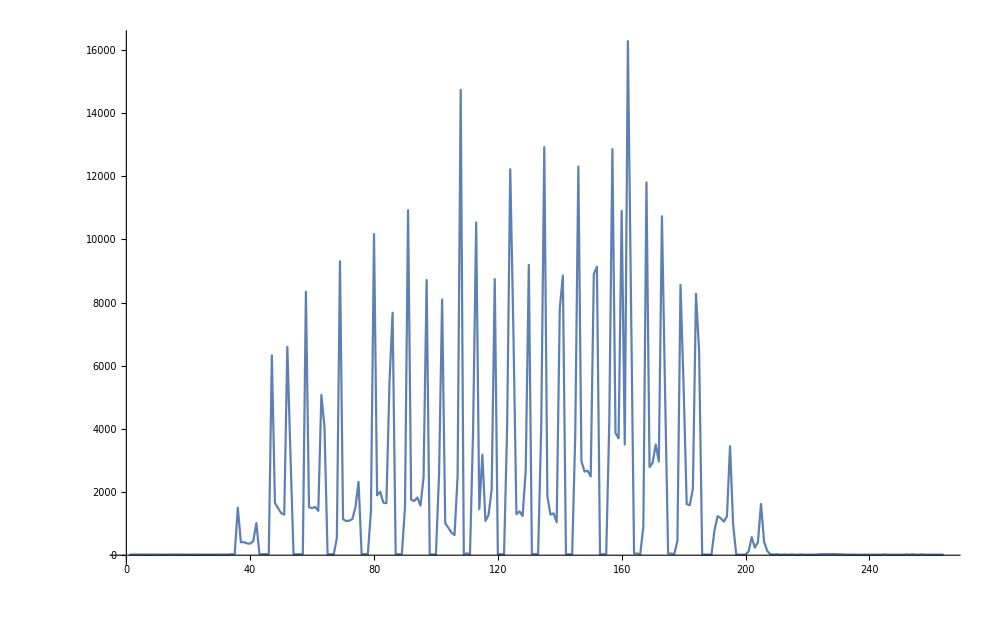

```mathematica
ListLinePlot[RefSpectrum[[All,1]],PlotRange->All,ImageSize->1000]
```

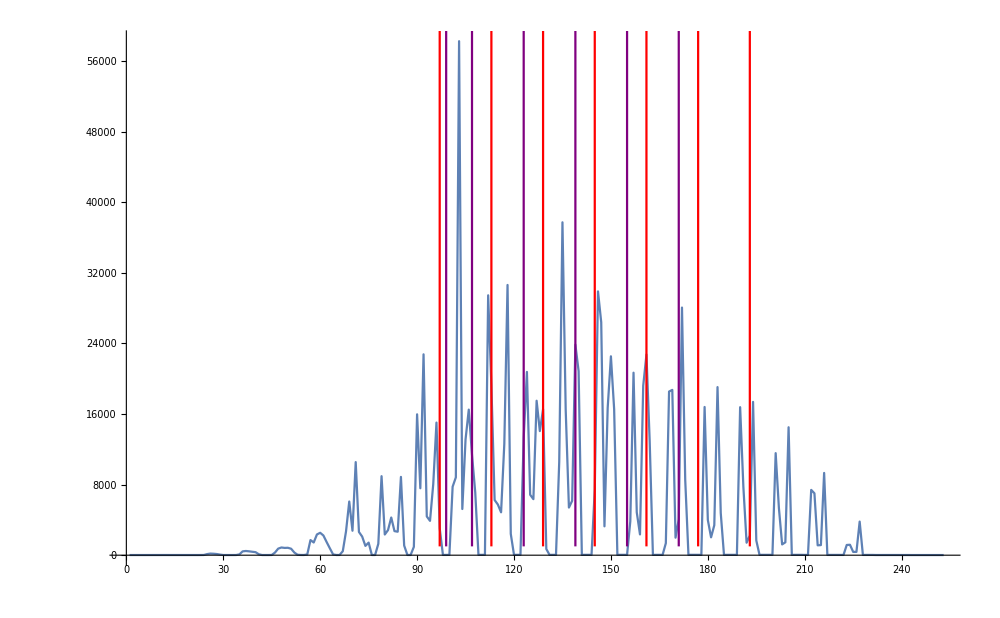

```mathematica
Show[
ListLinePlot[RefSpectrum[[All,1]],PlotRange->All,ImageSize->1000],
ParametricPlot[{{97,1000*d},{113,1000*d},{129,1000*d},{145,1000*d},{161,1000*d},{177,1000*d},{193,1000*d}},{d,1,253},PlotStyle->Red],
ParametricPlot[{{99,1000*d},{107,1000*d},{123,1000*d},{139,1000*d},{155,1000*d},{171,1000*d}},{d,1,253},PlotStyle->Purple]
]
```

## get Bin data

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
(xStart-xEnd)/24
```

-0.001875

```mathematica
xyBins[[1]]
```

{{0.025,0.02625},{-0.02,-0.015909}}

```mathematica
MCFolder="~/ClusterMC_v4/NoMoS_Danfysik_25-02-19_reduceTypes_smallerDV4/";
```

```mathematica
DetHisto={{-0.06999999999999999,-0.06499999999999999,-0.05999999999999999,-0.05499999999999999,-0.04999999999999999,-0.04499999999999999,-0.039999999999999994,-0.03499999999999999,-0.029999999999999992,-0.024999999999999994,-0.01999999999999999,-0.014999999999999993,-0.009999999999999995,-0.0049999999999999906,1.3877787807814457*^-17,0.0050000000000000044,0.010000000000000009,0.015000000000000013,0.020000000000000004,0.02500000000000001,0.030000000000000013,0.035,0.04000000000000001,0.045},{-1.0540019999999999,-1.049002,-1.0440019999999999,-1.039002,-1.0340019999999999,-1.029002,-1.0240019999999999,-1.019002,-1.0140019999999998,-1.009002,-1.0040019999999998,-0.9990019999999998,-0.9940019999999998,-0.9890019999999999,-0.9840019999999998,-0.9790019999999999,-0.9740019999999999,-0.9690019999999999,-0.9640019999999999,-0.9590019999999999,-0.9540019999999999,-0.9490019999999999,-0.9440019999999999},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,4,5,5,8,10,8,8,6,7,1,2,0,0,0,0,0,0,0},{0,0,0,2,10,21,53,53,54,70,54,58,46,21,8,3,0,0,0,0,0,0},{0,0,0,25,53,139,172,225,286,295,273,228,180,97,55,19,2,0,0,0,0,0},{0,0,17,66,190,414,617,832,888,901,832,724,556,375,198,49,14,1,0,0,0,0},{0,1,34,175,526,986,1611,2023,2292,2277,2214,1873,1477,947,504,192,41,1,0,0,0,0},{0,3,88,369,1087,2197,3813,4904,5250,5381,5155,4475,3545,2138,1186,436,106,11,0,0,0,0},{0,1,110,696,1886,4112,7968,10086,11143,11228,10855,9519,7598,4390,2004,769,181,9,0,0,0,0},{0,1,155,916,2905,6920,14467,18151,19991,20436,19831,18072,14297,7701,3307,1174,253,12,0,0,0,0},{0,2,119,1170,3997,10330,22455,28438,30617,31268,30614,28053,23025,11808,4634,1437,214,3,0,0,0,0},{0,0,61,1027,4717,13435,30336,38438,41907,42599,41926,39417,31810,16031,5781,1657,145,0,0,0,0,0},{0,0,11,674,4489,15048,36916,46817,50520,51226,51068,48296,39189,18713,6111,1268,47,0,0,0,0,0},{0,0,0,280,3692,15404,40139,51198,53790,54718,55258,52828,43694,19608,5208,594,0,0,0,0,0,0},{0,0,0,34,2219,13116,38833,48711,51342,51399,52013,51454,43194,18067,3567,184,0,0,0,0,0,0},{0,0,0,1,804,9211,32451,41018,41357,42074,43057,43175,36185,13879,1648,15,0,0,0,0,0,0},{0,0,0,0,155,5049,22938,27689,28143,28324,29185,29578,26021,8580,399,0,0,0,0,0,0,0},{0,0,0,0,7,1882,12109,14079,14010,14468,14745,15047,13718,3798,44,0,0,0,0,0,0,0},{0,0,0,0,0,368,3929,4520,4297,4409,4603,4715,4490,1028,0,0,0,0,0,0,0,0},{0,0,0,0,0,18,475,491,468,537,499,557,553,111,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,4,0,0,1,0,1,4,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
InfoFile=Import[MCFolder<>"info.txt","Table"];
```

```mathematica
R=0.999002
```

0.999002

```mathematica
xyBins[[1,1]]
```

{0.025,0.02625}

```mathematica
Clear[BinCenters]
```

```mathematica
BinCenters[binTable_]:=Block[{resTable},resTable=Table[{(xyBins[[i,1,1]]+xyBins[[i,1,2]])/2,(xyBins[[i,2,1]]+xyBins[[i,2,2]])/2},{i,Length[binTable]}];Return[resTable]]
```

### Get XY Bins with Ybins halfed

```mathematica
XYBinBoundariesYHalf=Flatten[Table[
{
{DetHisto[[1,xi]],DetHisto[[1,xi+1]]},
{-DetHisto[[2,yi+2]]-R,-DetHisto[[2,yi]]-R}
},{xi,1,Length[DetHisto[[1]]]-1,1},{yi,1,Length[DetHisto[[2]]]-2,2}],1];
```

Part::partd: Part specification DetHisto⟦1⟧ is longer than depth of object.

Part::partd: Part specification DetHisto⟦2⟧ is longer than depth of object.

```mathematica
Length[XYBinBoundariesYHalf]
```

253

```mathematica
Get["NeutronBeam/XYBinIntBoundaries.m"]
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
XYBinCentersYHalf[[1]]
```

{0.025625,-0.0179545}

## check spectrum

```mathematica
Transfer3DPlot=ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}],BaseStyle->20,ImageSize->600,AxesLabel->{"x (m)","y (m)","Ĝ(x_bin,y_bin)"},InterpolationOrder->1]
```

-Graphics3D-

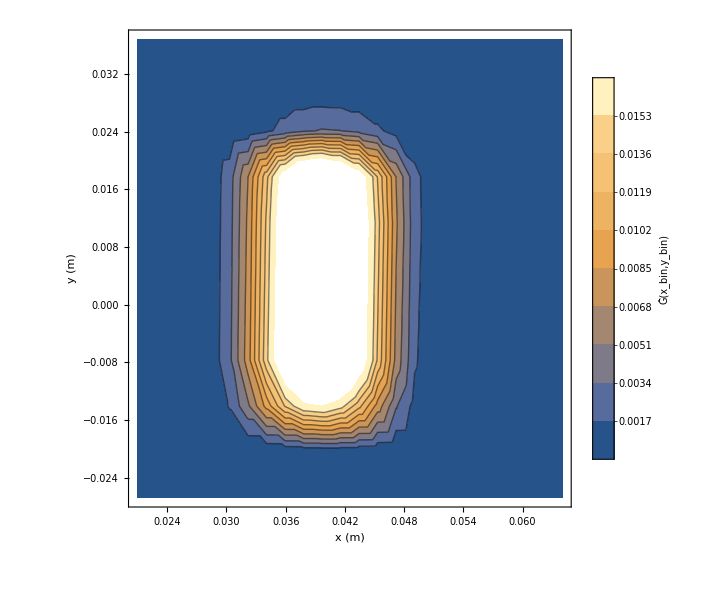

```mathematica
TransferContourPlot=ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

```mathematica
(*Export["~/Dropbox/PhD/PhDLatex/Figures/Transfer3D.png",Transfer3DPlot,ImageResolution->450];
Export["~/Dropbox/PhD/PhDLatex/Figures/TransferContour.png",TransferContourPlot,ImageResolution->450];*)
```

# dalpha, k=97.07

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dAlpha/a-1050/"];
```

```mathematica
dAlphaSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_179-264.txt}

```mathematica
dAlphaSpectruma0=Flatten[Table[Import[dAlphaSubFileNamesa0[[i]],"Table"],{i,1,Length[dAlphaSubFileNamesa0]}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma0[[All,2]]/Total[dAlphaSpectruma0[[All,2]]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dAlpha/a-1040/"];
```

```mathematica
dAlphaSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_179-264.txt}

```mathematica
dAlphaSpectruma1040=Flatten[Table[Import[dAlphaSubFileNamesa1040[[i]],"Table"],{i,1,Length[dAlphaSubFileNamesa1040]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1040[[All,2]]/Total[dAlphaSpectruma1040[[All,2]]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dAlpha/a-1045/"];
```

```mathematica
dAlphaSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_179-264.txt}

```mathematica
dAlphaSpectruma1045=Flatten[Table[Import[dAlphaSubFileNamesa1045[[i]],"Table"],{i,1,Length[dAlphaSubFileNamesa1045]}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dAlpha/a-1055/"];
```

```mathematica
dAlphaSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_179-264.txt}

```mathematica
dAlphaSpectruma1055=Flatten[Table[Import[dAlphaSubFileNamesa1055[[i]],"Table"],{i,1,Length[dAlphaSubFileNamesa1055]}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dAlpha/a-1060/"];
```

```mathematica
dAlphaSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dAlphaSpectruma1060=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesa1060,1];
```

```mathematica
dAlphaSpectruma1060[[All,2]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000114515,0.000184805,0.000179744,0.000174875,0.000170191,0.000165646,0.000010631,0.,0.,0.,0.,0.00208322,0.00335448,0.00326392,0.00317675,0.00309282,0.00299578,0.000207217,0.,0.,0.,0.,0.00929392,0.0149753,0.0145837,0.0142061,0.0138419,0.0132834,0.00105432,0.,0.,0.,7.85747×10^-6,0.0241814,0.0390404,0.0380869,0.0371627,0.0362673,0.0344372,0.00311712,0.,0.,0.,0.0000994742,0.0461065,0.0749538,0.073444,0.0719523,0.0704979,0.0663773,0.00696375,0.,0.,0.,0.000359707,0.0695109,0.114023,0.112425,0.110812,0.109204,0.102377,0.0118254,0.,0.,0.,0.000644083,0.086333,0.142981,0.141995,0.140934,0.139836,0.131063,0.016007,0.,0.,0.,0.000818567,0.0897408,0.149729,0.1496,0.149415,0.149195,0.139876,0.0179104,0.,0.,0.,0.000872587,0.0811859,0.136282,0.136895,0.137409,0.137896,0.129115,0.0173718,0.,0.,0.,0.000845437,0.0628334,0.106529,0.10785,0.109074,0.110264,0.103298,0.0146209,0.,0.,0.,0.000667292,0.0393762,0.06762,0.0693104,0.0709273,0.0725289,0.068283,0.0101124,0.,0.,0.,0.000346991,0.0180153,0.0314942,0.0329486,0.0343894,0.035846,0.0341913,0.00540924,0.,0.,0.,0.0000759947,0.00552551,0.00980404,0.0104646,0.0111522,0.0118759,0.0114018,0.0019883,0.,0.,0.,2.96194×10^-6,0.00121318,0.00217354,0.00237672,0.00259275,0.00282247,0.00277463,0.000475478,0.,0.,0.,0.,0.000116968,0.000221071,0.000258751,0.000300942,0.000348035,0.000369349,0.0000579729,0.,0.,0.,0.,8.80772×10^-7,2.11344×10^-6,3.21047×10^-6,4.59463×10^-6,6.53823×10^-6,8.64622×10^-6,1.15482×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1060[[All,2]]/Total[dAlphaSpectruma1060[[All,2]]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dAlphaSpectruma0[[All,2]]/Total[dAlphaSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,xStart,xEnd},{y,yStart,yEnd},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.0200032,-0.029995} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

```mathematica
dBRxBSpectrumb0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma0[[All,2]]/Total[dAlphaSpectruma0[[All,2]]]}]];
```

InterpolatingFunction::dmval: Input value {0.0200009,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

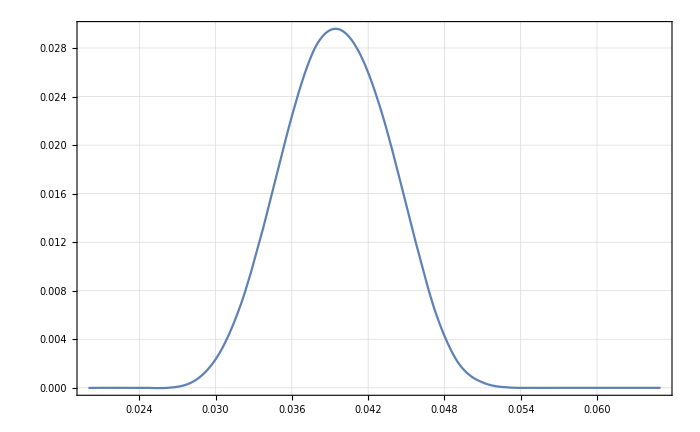

```mathematica
Plot[RefSpectrumInter[x,0.],{x,xStart,xEnd},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.0200009,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

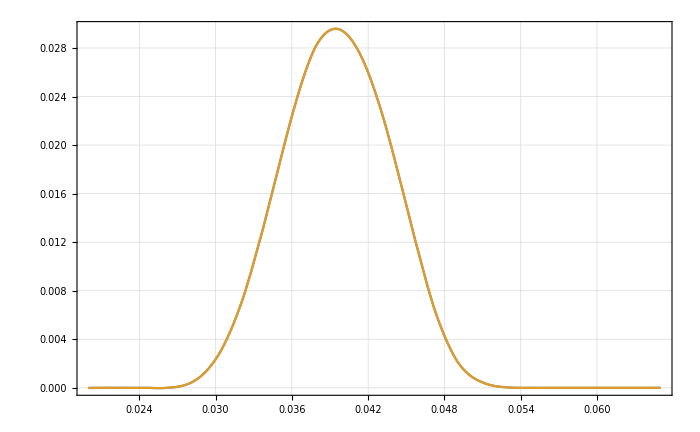

```mathematica
Plot[{RefSpectrumInter[x,0.],dBRxBSpectrumb0Inter[x,0.]},{x,xStart,xEnd},PlotRange->All]
```

```mathematica
dBRxBSpectrumb75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1040[[All,2]]/Total[dAlphaSpectruma1040[[All,2]]]}]];
dBRxBSpectrumbm75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1045[[All,2]]/Total[dAlphaSpectruma1045[[All,2]]]}]];
dBRxBSpectrumb15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1055[[All,2]]/Total[dAlphaSpectruma1055[[All,2]]]}]];
dBRxBSpectrumbm15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1060[[All,2]]/Total[dAlphaSpectruma1060[[All,2]]]}]];
```

InterpolatingFunction::dmval: Input value {0.0200009,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

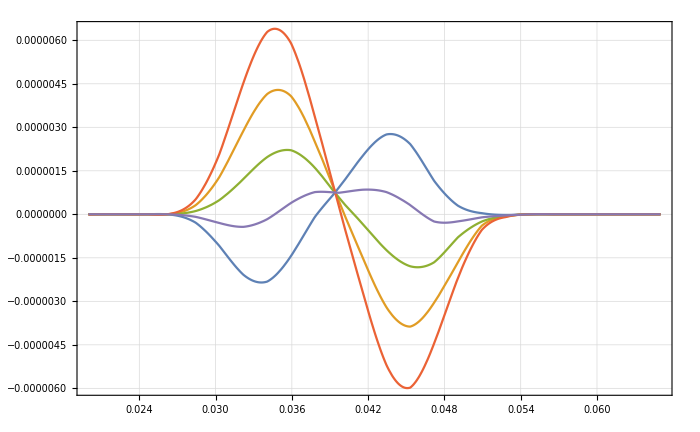

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dBRxBSpectrumbm15Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumbm75Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumb0Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumb75Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumb15Inter[x,0.]
}
,{x,xStart,xEnd},PlotRange->All]
```

```mathematica
ListPlot[Total[(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-#)^2]&/@BRxBDataList]
```

ListPlot::lpn: BRxBDataList is not a list of numbers or pairs of numbers.

ListPlot[BRxBDataList]

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFit]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
AlphaDataList={dAlphaSpectruma1040[[All,2]]/Total[dAlphaSpectruma1040[[All,2]]],dAlphaSpectruma1045[[All,2]]/Total[dAlphaSpectruma1045[[All,2]]],dAlphaSpectruma0[[All,2]]/Total[dAlphaSpectruma0[[All,2]]],dAlphaSpectruma1055[[All,2]]/Total[dAlphaSpectruma1055[[All,2]]],dAlphaSpectruma1060[[All,2]]/Total[dAlphaSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
dAlphaSpectruma1040[[All,2]]//Length
```

362

```mathematica
dAlphaSpectruma1055[[All,2]]//Length
```

264

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

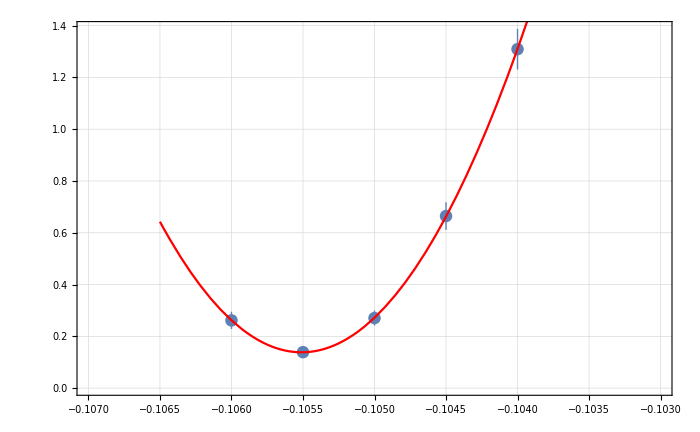
{{{1.30928×10^-9,6.64616×10^-10,2.70495×10^-10,1.38769×10^-10,2.61511×10^-10},{7.86811×10^-11,5.31884×10^-11,2.90487×10^-11,1.67193×10^-11,3.31935×10^-11}},a0 =  | -0.10551
FittedModel[1.38332×10^-10+0.000514142 (0.10551+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.10551 | 0.0000414574 | -2545.01 | 1.5439×10^-7
scale | 0.000514142 | 0.000043962 | 11.6952 | 0.00723196
yoffset | 1.38332×10^-10 | 1.41633×10^-11 | 9.76692 | 0.010321 | 
 | DF | SS | MS
Model | 3 | 650.7 | 216.9
Error | 2 | 0.00474935 | 0.00237467
Uncorrected Total | 5 | 650.705 | 
Corrected Total | 4 | 286.56 |  | ,-Graphics-}

```mathematica
AlphaInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],AlphaDataList,bList, 4]
```

```mathematica
(-0.1055096205659537+0.105)/-0.105
```

0.00485353

```mathematica
-0.105+(0.105*0.01)
```

-0.10395

```mathematica
-0.1042255483567612
```

```mathematica
AlphaInvest[[2,1,1,2]]
```

-0.10551

```mathematica
(AlphaInvest[[2,1,1,2]]+0.105)/(-0.105)/(5*10^-5)
```

97.0706

```mathematica
0.004853529199559075/(5*10^-5)
```

97.0706

# drF, k=4.43

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drF/a-1050/"];
```

```mathematica
drFSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_drF_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_179-264.txt}

```mathematica
drFSpectruma0=Flatten[Table[Import[drFSubFileNamesa0[[i]],"Table"],{i,1,Length[drFSubFileNamesa0]}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drF/a-1040/"];
```

```mathematica
drFSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drF_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_179-264.txt}

```mathematica
drFSpectruma1040=Flatten[Import[#,"Table"]&/@drFSubFileNamesa1040,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drF/a-1045/"];
```

```mathematica
drFSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_drF_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_179-264.txt}

```mathematica
drFSpectruma1045=Flatten[Import[#,"Table"]&/@drFSubFileNamesa1045,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drF/a-1055/"];
```

```mathematica
drFSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_drF_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_179-264.txt}

```mathematica
drFSpectruma1055=Flatten[Import[#,"Table"]&/@drFSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

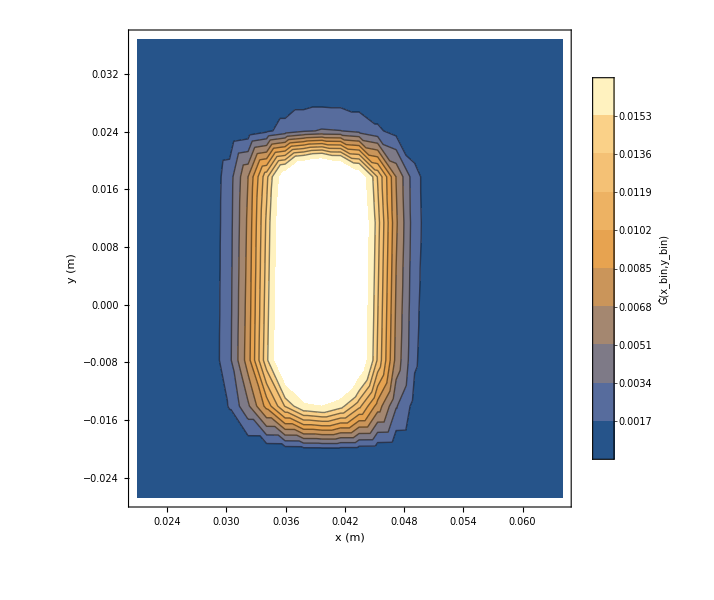

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1055[[All,2]]/Total[drFSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drF/a-1060/"];
```

```mathematica
drFSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drF_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drFSpectruma1060=Flatten[Import[#,"Table"]&/@drFSubFileNamesa1060,1];
```

```mathematica
drFSpectruma1055[[All,2]]//Length
```

264

```mathematica
drFSpectruma1060[[All,2]]//Length
```

256

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1060[[All,2]]}],PlotRange->All]
```

Transpose::nmtx: The first two levels of {{0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,«11»,0.028125,0.028125,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,«214»},{«1»},{«1»}} cannot be transposed.

ListPlot3D::arrayerr: Transpose[{«1»}] must be a valid array or a list of valid arrays.

ListPlot3D[Transpose[{{0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375},{-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225},{0.,4.47425×10^-7,6.02744×10^-7,5.91973×10^-7,5.81468×10^-7,5.71224×10^-7,5.61233×10^-7,5.51489×10^-7,5.41986×10^-7,5.32718×10^-7,4.75389×10^-8,0.,0.0000879969,0.000119268,0.000117147,0.000115078,0.000113059,0.000111091,0.00010917,0.000107297,0.00010543,0.0000104977,0.,0.000701745,0.000952878,0.00093608,0.000919691,0.000903701,0.000888099,0.000872877,0.000858025,0.000839179,0.0000834952,3.5836×10^-6,0.00239433,0.00325997,0.00320344,0.00314825,0.00309437,0.00304178,0.00299043,0.00294031,0.00284975,0.000327453,0.000037155,0.00559804,0.00767238,0.00754283,0.00741622,0.0072925,0.00717161,0.00705348,0.00693807,0.00664837,0.000848306,0.000165113,0.0105384,0.0145972,0.0143612,0.0141301,0.0139039,0.0136825,0.0134658,0.0132537,0.0125429,0.00178018,0.000466438,0.0171219,0.0240336,0.0236801,0.0233297,0.022985,0.0226459,0.0223126,0.021985,0.0205558,0.00321438,0.00096978,0.0246906,0.0351399,0.0347259,0.0342925,0.0338625,0.0334367,0.0330126,0.0325974,0.0301499,0.00514795,0.00159149,0.0322596,0.0464223,0.0460451,0.0455901,0.0451366,0.0446842,0.0442341,0.0437851,0.0401522,0.0544281,0.0540196,0.0492595,0.00942923,0.00266363,0.0428271,0.0626197,0.0626168,0.0623765,0.0621288,0.0618731,0.0616107,0.0613375,0.05573,0.011033,0.00295451,0.0436845,0.0643068,0.0645062,0.0644428,0.06436,0.0642704,0.064177,0.0640722,0.0580227,0.0118582,0.00307535,0.0419021,0.0620969,0.0624748,0.062525,0.0625699,0.0626116,0.062647,0.0626745,0.0564962,0.0119396,0.00302753,0.0378254,0.056474,0.0569931,0.0571759,0.0573524,0.0575234,0.057676,0.0578325,0.0519097,0.0113495,0.00278236,0.0317647,0.0478165,0.0484712,0.0487879,0.0490987,0.0494035,0.049702,0.0499907,0.0446863,0.010074,0.00232516,0.0244053,0.0370302,0.0377635,0.0381813,0.0385945,0.0390033,0.0394075,0.0398029,0.0354729,0.00833864,0.00171419,0.0167922,0.0256606,0.0263695,0.0268248,0.0272801,0.0277306,0.0281806,0.0286239,0.0254997,0.00619068,0.00108409,0.0098629,0.015269,0.015852,0.0162725,0.0166946,0.0171238,0.0175441,0.0179669,0.0160051,0.00404876,0.000562323,0.00473851,0.00745261,0.00782324,0.00811736,0.00841886,0.00872724,0.00904185,0.00936082,0.00832003,0.00225943,0.000226292,0.00197739,0.00313934,0.00331034,0.00345557,0.00360644,0.00376261,0.00392418,0.0040914,0.00361137,0.00103357,0.0000710994,0.000718059,0.00114017,0.00121167,0.00127949,0.00135001,0.00142319,0.00149911,0.00157783,0.00141378,0.000393956,0.0000121256,0.000189393,0.000301593,0.000326884,0.000353033,0.000380663,0.000409764,0.000440381,0.000472558,0.000439617,0.00011556,4.52877×10^-7,0.0000258848,0.0000418482,0.0000476277,0.0000539891,0.0000609723,0.000068562,0.0000768318,0.0000858192,0.0000850529,0.0000185858,0.,6.46386×10^-7,1.16186×10^-6,1.71743×10^-6,2.60735×10^-6,2.55523×10^-6,3.22825×10^-6,4.01108×10^-6,5.00119×10^-6,5.74377×10^-6,1.0528×10^-6}}],PlotRange→All]

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumbm15[[All,2]]/Total[dBRxBSpectrumbm15[[All,2]]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dBRxBSpectrumb0[[All,2]]/Total[dBRxBSpectrumb0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.0250021,-0.0199964} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

```mathematica
drFSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma0[[All,2]]/Total[drFSpectruma0[[All,2]]]}]];
```

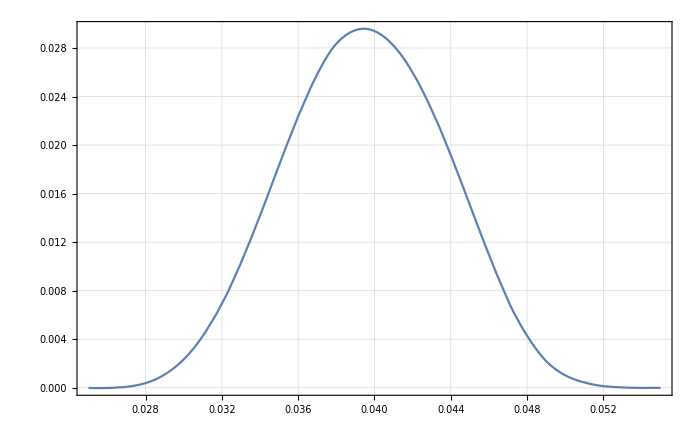

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

```mathematica
drFSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1040[[All,2]]/Total[drFSpectruma1040[[All,2]]]}]];
drFSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1045[[All,2]]/Total[drFSpectruma1045[[All,2]]]}]];
drFSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1055[[All,2]]/Total[drFSpectruma1055[[All,2]]]}]];
```

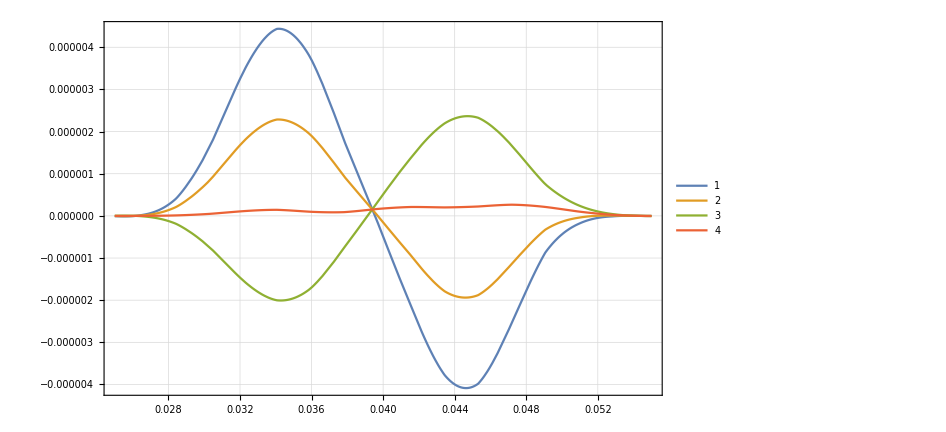

```mathematica
Plot[{
RefSpectrumInter[x,0.]-drFSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-drFSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-drFSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-drFSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
rFDataList={drFSpectruma1040[[All,2]]/Total[drFSpectruma1040[[All,2]]],drFSpectruma1045[[All,2]]/Total[drFSpectruma1045[[All,2]]],drFSpectruma0[[All,2]]/Total[drFSpectruma0[[All,2]]],drFSpectruma1055[[All,2]]/Total[drFSpectruma1055[[All,2]]],drFSpectruma1060[[All,2]]/Total[drFSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

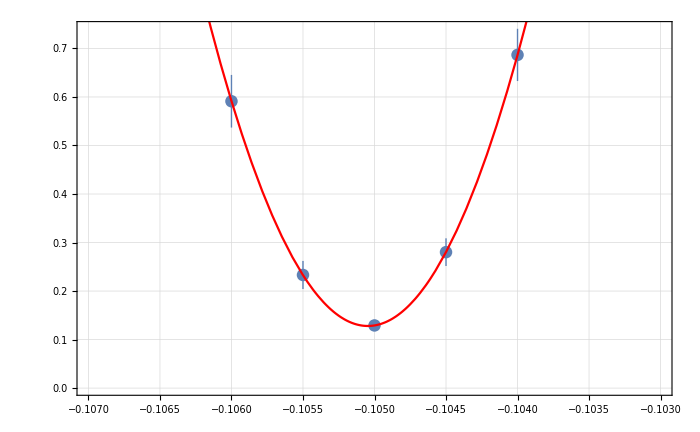
{{{6.86703×10^-10,2.80175×10^-10,1.29136×10^-10,2.33128×10^-10,5.91184×10^-10},{5.38263×10^-11,2.85119×10^-11,1.12789×10^-11,2.89544×10^-11,5.42352×10^-11}},a0 =  | -0.105047
FittedModel[1.28043×10^-10+0.000509836 (0.105047+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105047 | 0.0000275451 | -3813.62 | 6.87583×10^-8
scale | 0.000509836 | 0.0000382191 | 13.3398 | 0.0055726
yoffset | 1.28043×10^-10 | 1.06022×10^-11 | 12.077 | 0.00678645 | 
 | DF | SS | MS
Model | 3 | 574.056 | 191.352
Error | 2 | 0.000169658 | 0.0000848291
Uncorrected Total | 5 | 574.056 | 
Corrected Total | 4 | 181.206 |  | ,-Graphics-}

```mathematica
rFInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],rFDataList,bList, 4]
```

```mathematica
(rFInvest[[2,1,1,2]]+0.105)/-0.105
```

0.000442949

```mathematica
0.000442948920583481/(10^-4)
```

4.42949

# drA, k=95.24

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1050/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_G_drA_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1050_179-264.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1040/"];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1040/Cluster_Try"];
```

```mathematica
drASubFileNamesa1040Cluster=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_179-264.txt}

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_drA_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_G_drA_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_G_drA_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_G_drA_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_G_drA_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_G_drA_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_G_drA_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_G_drA_a-1040_179-264.txt}

```mathematica
drASpectruma1040Cluster=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040Cluster,1];
```

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1045/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_drA_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_179-264.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1055/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_179-264.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

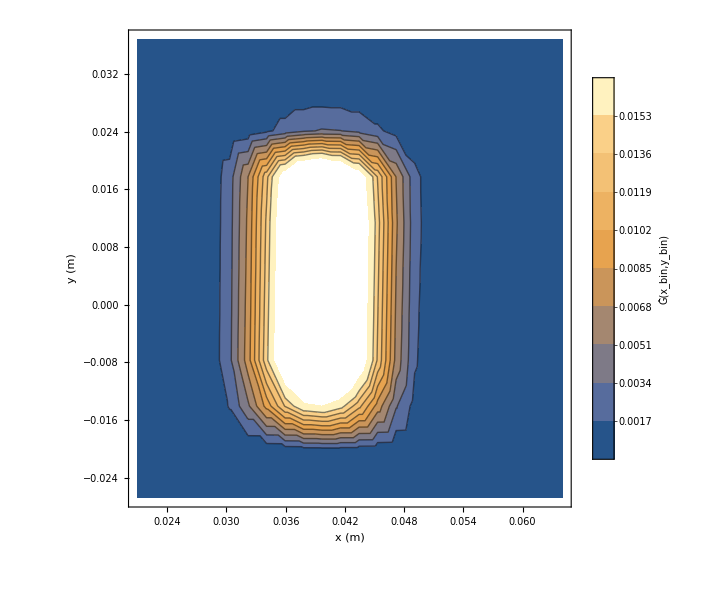

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1060/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
drASpectruma1040InterCluster=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1040Cluster[[All,2]]/Total[drASpectruma1040Cluster[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

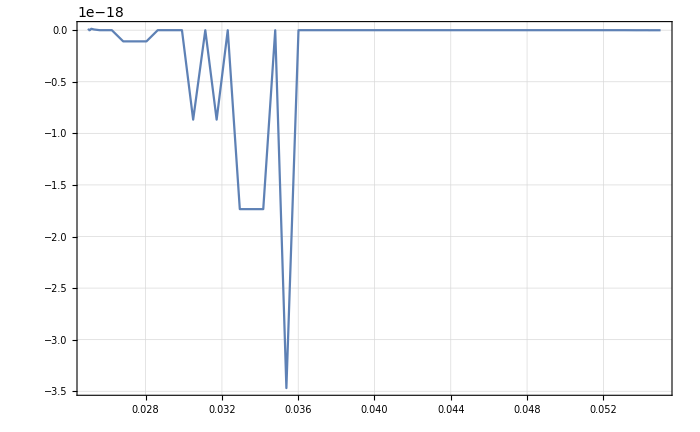

```mathematica
Plot[drASpectruma1040Inter[x,0.]-drASpectruma1040InterCluster[x,0.],{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
1.97*10^-3
```

0.00197

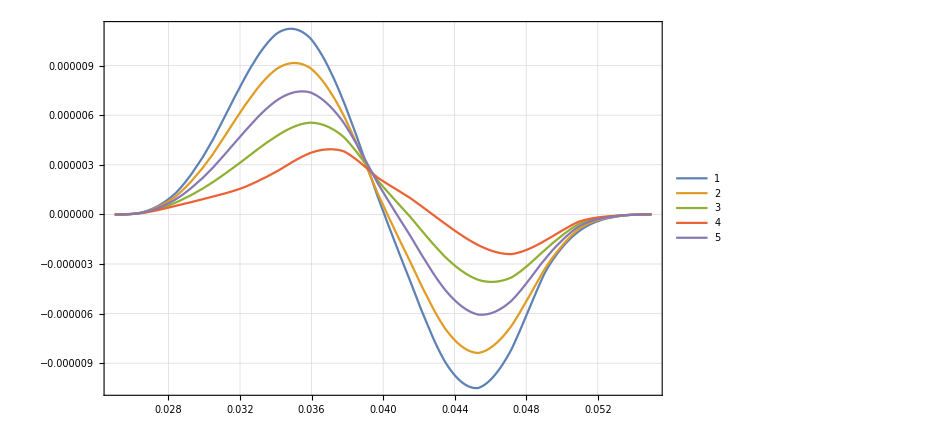

```mathematica
Plot[{
RefSpectrumInter[x,0.]-drASpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-drASpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-drASpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-drASpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-drASpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

### a=-1065

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1065/"];
```

```mathematica
drASubFileNamesa1065=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1065_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1065=Flatten[Import[#,"Table"]&/@drASubFileNamesa1065,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1065[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1070

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1070/"];
```

```mathematica
drASubFileNamesa1070=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1070_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1070=Flatten[Import[#,"Table"]&/@drASubFileNamesa1070,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1070[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1075

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1075/"];
```

```mathematica
drASubFileNamesa1075=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1075_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1075=Flatten[Import[#,"Table"]&/@drASubFileNamesa1075,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1075[[All,2]]}],PlotRange->All]
```

-Graphics3D-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]],drASpectruma1065[[All,2]]/Total[drASpectruma1065[[All,2]]],drASpectruma1070[[All,2]]/Total[drASpectruma1070[[All,2]]],drASpectruma1075[[All,2]]/Total[drASpectruma1075[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060,-0.1065,-0.1070,-0.1075}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106,-0.1065,-0.107,-0.1075}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

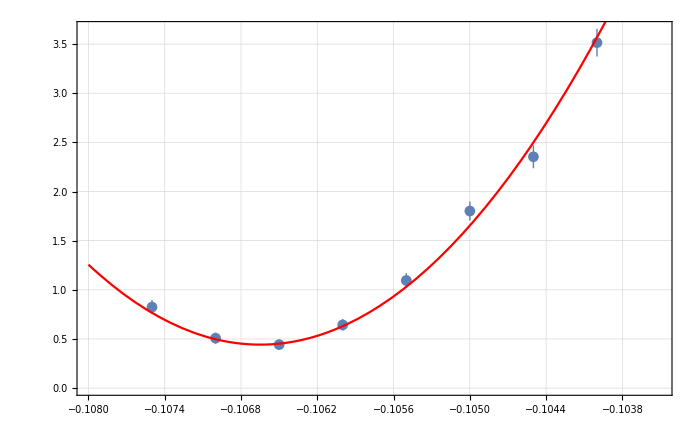
{{{3.51471×10^-9,2.35326×10^-9,1.80157×10^-9,1.09474×10^-9,6.43061×10^-10,4.42288×10^-10,5.07741×10^-10,8.24147×10^-10},{1.40892×10^-10,1.16125×10^-10,9.64692×10^-11,7.53158×10^-11,5.8544×10^-11,5.08038×10^-11,5.64233×10^-11,7.15789×10^-11}},a0 =  | -0.106649
FittedModel[4.42288×10^-10+0.000445521 (0.106649+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106649 | 0.0000513687 | -2076.14 | 4.92061×10^-16
scale | 0.000445521 | 0.0000263228 | 16.9253 | 0.000013168
yoffset | 4.42288×10^-10 | 2.94575×10^-11 | 15.0145 | 0.0000237319 | 
 | DF | SS | MS
Model | 3 | 1997.37 | 665.79
Error | 5 | 5.62228 | 1.12446
Uncorrected Total | 8 | 2002.99 | 
Corrected Total | 7 | 744.691 |  | ,-Graphics-}

```mathematica
rAInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],rADataList,bList, 4]
```

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

157.014

# dB, k=69.93

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dB/a-1050/"];
```

```mathematica
dBSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dB_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_179-264.txt}

```mathematica
dBSpectruma0=Flatten[Table[Import[dBSubFileNamesa0[[i]],"Table"],{i,1,Length[dBSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dB/a-1040/"];
```

```mathematica
dBSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dB_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_179-264.txt}

```mathematica
dBSpectruma1040=Flatten[Import[#,"Table"]&/@dBSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dB/a-1045/"];
```

```mathematica
dBSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dB_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_179-264.txt}

```mathematica
dBSpectruma1045=Flatten[Import[#,"Table"]&/@dBSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dB/a-1055/"];
```

```mathematica
dBSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dB_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_179-264.txt}

```mathematica
dBSpectruma1055=Flatten[Import[#,"Table"]&/@dBSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

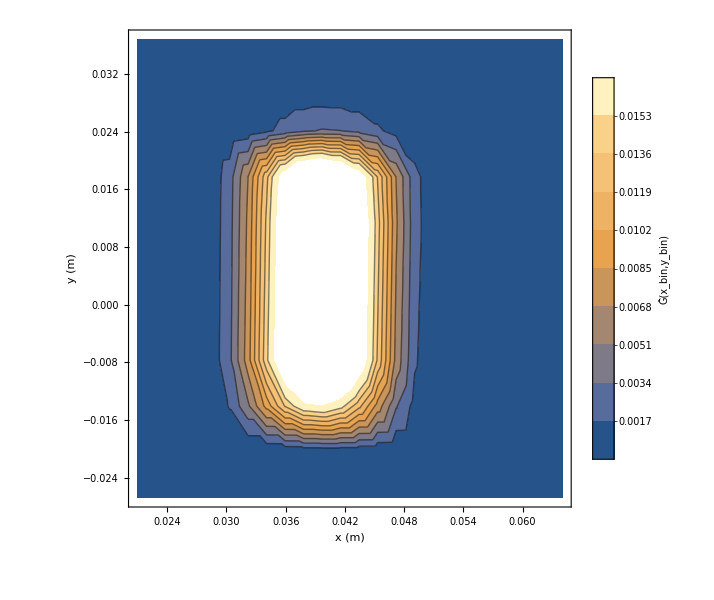

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1055[[All,2]]/Total[dBSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dB/a-1060/"];
```

```mathematica
dBSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dB_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dBSpectruma1060=Flatten[Import[#,"Table"]&/@dBSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dBSpectruma0[[All,2]]/Total[dBSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dBSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma0[[All,2]]/Total[dBSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dBSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1040[[All,2]]/Total[dBSpectruma1040[[All,2]]]}]];
dBSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1045[[All,2]]/Total[dBSpectruma1045[[All,2]]]}]];
dBSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1055[[All,2]]/Total[dBSpectruma1055[[All,2]]]}]];
dBSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1060[[All,2]]/Total[dBSpectruma1060[[All,2]]]}]];
```

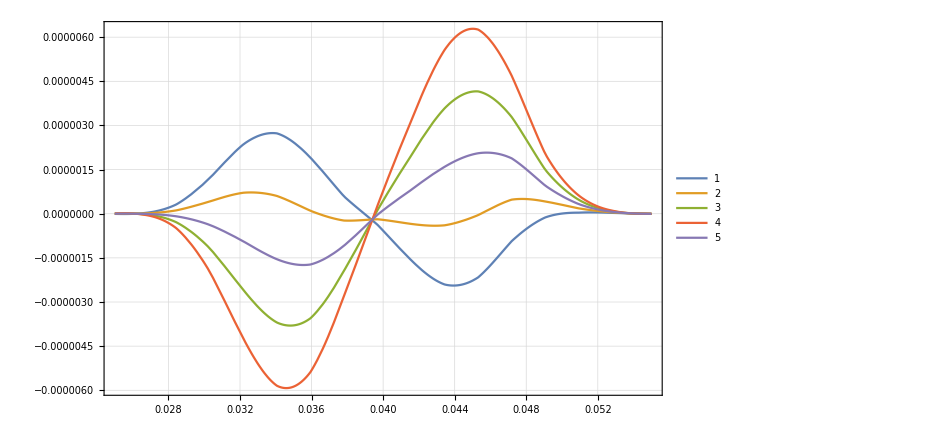

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dBSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dBSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dBSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dBSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dBSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
BDataList={dBSpectruma1040[[All,2]]/Total[dBSpectruma1040[[All,2]]],dBSpectruma1045[[All,2]]/Total[dBSpectruma1045[[All,2]]],dBSpectruma0[[All,2]]/Total[dBSpectruma0[[All,2]]],dBSpectruma1055[[All,2]]/Total[dBSpectruma1055[[All,2]]],dBSpectruma1060[[All,2]]/Total[dBSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

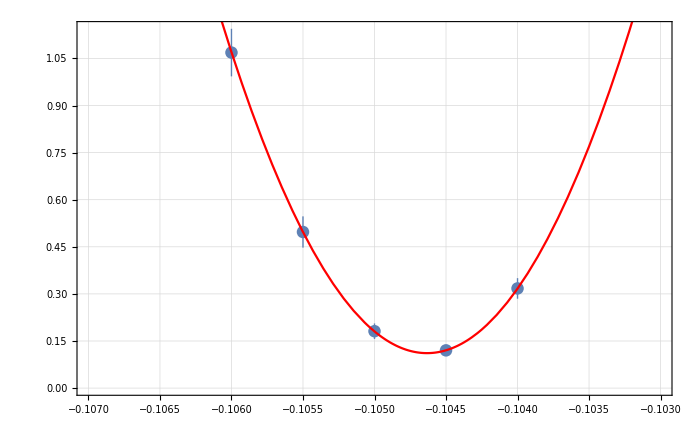
{{{3.17415×10^-10,1.20191×10^-10,1.81208×10^-10,4.97177×10^-10,1.06859×10^-9},{3.27248×10^-11,1.16634×10^-11,2.47023×10^-11,4.97713×10^-11,7.57612×10^-11}},a0 =  | -0.104633
FittedModel[1.11361×10^-10+0.000512848 (0.104633+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104633 | 0.00003187 | -3283.12 | 9.27742×10^-8
scale | 0.000512848 | 0.0000411871 | 12.4517 | 0.00638805
yoffset | 1.11361×10^-10 | 1.1474×10^-11 | 9.70545 | 0.0104501 | 
 | DF | SS | MS
Model | 3 | 552.813 | 184.271
Error | 2 | 0.00192816 | 0.000964081
Uncorrected Total | 5 | 552.815 | 
Corrected Total | 4 | 222.042 |  | ,-Graphics-}

```mathematica
BInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],BDataList,bList, 4]
```

```mathematica
.106*6.930
```

0.73458

```mathematica
.75*.1
```

0.075

```mathematica
.15*69.93
```

10.4895

```mathematica
.15*69.93
```

10.4895

```mathematica
(BInvest[[2,1,1,2]]+0.105)/-0.105
```

-0.00349668

```mathematica
-0.003496680950444102/(5*10^-5)
```

-69.9336

```mathematica
.1*97.07
```

9.707

```mathematica
Sqrt[10.489500000000001^2+9.707^2]
```

14.2918

```mathematica
14*10^-3.
```

0.014

```mathematica
%*100
```

1.4

```mathematica
18*4
```

72

```mathematica
1/7.83
```

0.127714